```mathematica
(* Note that this code works in dimensionless variables A(ρ), F(ρ) *)
(* These are related to the variables in the companion paper via ρ = r√(3Subscript[λM, P]^2/8π), A = R√(3Subscript[λM, P]^2/8π), F = f√(8π/3 Subscript[M, P]^2) *)
ClearAll["Global'*"];
SetDirectory[NotebookDirectory[]];
<<u1.m; (* Import package u1.m *)
λ = 0.1; (* Choose quartic coupling *)
```

Successfully loaded u1.m

```mathematica
{fa }= {10^16 GeV}; (* Set decay constant *)
```

```mathematica
IterateSolver[λ, fa, 40]; (* Find the correct initial condition for F(0) and solve for the dynamics *)
(* Note that this may take a while. If Subscript[ρ, max] > O(1000), then you can safely abort the loop and plot the results *)
```

Run 1: F(0) = 1.75, ρ_max = 1.2663

F'(ρ_max) = 2.61392×10^6, A'(ρ_max) = 0.98388

Run 2: F(0) = 1.125, ρ_max = 13.630

F'(ρ_max) = 3.26397×10^10, A'(ρ_max) = 0.99982

Run 3: F(0) = 0.8125, ρ_max = 0.061001

F'(ρ_max) = -0.557057, A'(ρ_max) = 0.91246

Run 4: F(0) = 0.96875, ρ_max = 0.099177

F'(ρ_max) = -0.556277, A'(ρ_max) = 0.98001

Run 5: F(0) = 1.046875, ρ_max = 0.16107

F'(ρ_max) = -0.5558, A'(ρ_max) = 0.99599

Run 6: F(0) = 1.085938, ρ_max = 0.28041

F'(ρ_max) = -1.84906, A'(ρ_max) = 0.99942

Run 7: F(0) = 1.105469, ρ_max = 0.74209

F'(ρ_max) = -0.306482, A'(ρ_max) = 0.99998

Run 8: F(0) = 1.115234, ρ_max = 22.764

F'(ρ_max) = 3.26039×10^10, A'(ρ_max) = 0.99994

Run 9: F(0) = 1.110352, ρ_max = 53.639

F'(ρ_max) = 3.5141×10^10, A'(ρ_max) = 0.99999

Run 10: F(0) = 1.10791, ρ_max = 1.2808

F'(ρ_max) = -0.10689, A'(ρ_max) = 1.

Run 11: F(0) = 1.109131, ρ_max = 5.4742

F'(ρ_max) = -0.00609232, A'(ρ_max) = 1.

Run 12: F(0) = 1.109741, ρ_max = 78.906

F'(ρ_max) = 3.04697×10^10, A'(ρ_max) = 0.99999

Run 13: F(0) = 1.109436, ρ_max = 120.68

F'(ρ_max) = 4.05658×10^10, A'(ρ_max) = 1.

Run 14: F(0) = 1.109283, ρ_max = 207.57

F'(ρ_max) = 3.10971×10^10, A'(ρ_max) = 1.

Run 15: F(0) = 1.109207, ρ_max = 1310.3

F'(ρ_max) = 3.47997×10^10, A'(ρ_max) = 1.

Run 16: F(0) = 1.109169, ρ_max = 7.9369

F'(ρ_max) = -0.0029094, A'(ρ_max) = 1.

Run 17: F(0) = 1.109188, ρ_max = 11.830

F'(ρ_max) = -0.00131336, A'(ρ_max) = 1.

Run 18: F(0) = 1.109198, ρ_max = 18.951

F'(ρ_max) = -0.00051289, A'(ρ_max) = 1.

Run 19: F(0) = 1.109202, ρ_max = 40.740

F'(ρ_max) = -0.000111223, A'(ρ_max) = 1.

Run 20: F(0) = 1.109205, ρ_max = 1774.4

F'(ρ_max) = -4.86751×10^-7, A'(ρ_max) = 1.

Run 21: F(0) = 1.109206, ρ_max = 2490.9

F'(ρ_max) = -1.00567×10^-7, A'(ρ_max) = 1.

Run 22: F(0) = 1.109207, ρ_max = 1640.2

F'(ρ_max) = 6.84348×10^11, A'(ρ_max) = 1.

Run 23: F(0) = 1.109206, ρ_max = 2037.3

F'(ρ_max) = 2.27869×10^10, A'(ρ_max) = 1.

Run 24: F(0) = 1.109206, ρ_max = 2744.0

F'(ρ_max) = 7.19375×10^9, A'(ρ_max) = 1.

Run 25: F(0) = 1.109206, ρ_max = 2794.3

F'(ρ_max) = -5.04906×10^-8, A'(ρ_max) = 1.

Run 26: F(0) = 1.109206, ρ_max = 3306.2

F'(ρ_max) = -1.61893×10^-8, A'(ρ_max) = 1.

Run 27: F(0) = 1.109206, ρ_max = 3150.6

F'(ρ_max) = 2.21575×10^11, A'(ρ_max) = 1.

Run 28: F(0) = 1.109206, ρ_max = 4373.5

F'(ρ_max) = -1.65153×10^-9, A'(ρ_max) = 1.

Run 29: F(0) = 1.109206, ρ_max = 3409.7

F'(ρ_max) = 2.44477×10^11, A'(ρ_max) = 1.

Run 30: F(0) = 1.109206, ρ_max = 3681.2

F'(ρ_max) = 2.06408×10^11, A'(ρ_max) = 1.

Run 31: F(0) = 1.109206, ρ_max = 3988.8

F'(ρ_max) = 3.12913×10^11, A'(ρ_max) = 1.

Run 32: F(0) = 1.109206, ρ_max = 4427.5

F'(ρ_max) = 1.49373×10^11, A'(ρ_max) = 1.

Run 33: F(0) = 1.109206, ρ_max = 4893.1

F'(ρ_max) = -5.65602×10^-10, A'(ρ_max) = 1.

Run 34: F(0) = 1.109206, ρ_max = 4794.3

F'(ρ_max) = 4.35831×10^9, A'(ρ_max) = 1.

Run 35: F(0) = 1.109206, ρ_max = 6744.1

F'(ρ_max) = -1.47273×10^-11, A'(ρ_max) = 1.

Run 36: F(0) = 1.109206, ρ_max = 5024.5

F'(ρ_max) = 1.32887×10^11, A'(ρ_max) = 1.

Run 37: F(0) = 1.109206, ρ_max = 5254.5

F'(ρ_max) = 1.14731×10^11, A'(ρ_max) = 1.

Run 38: F(0) = 1.109206, ρ_max = 5485.4

F'(ρ_max) = 9.82313×10^10, A'(ρ_max) = 1.

Run 39: F(0) = 1.109206, ρ_max = 5719.6

F'(ρ_max) = 1.43822×10^11, A'(ρ_max) = 1.

Run 40: F(0) = 1.109206, ρ_max = 5961.8

F'(ρ_max) = 1.42167×10^11, A'(ρ_max) = 1.

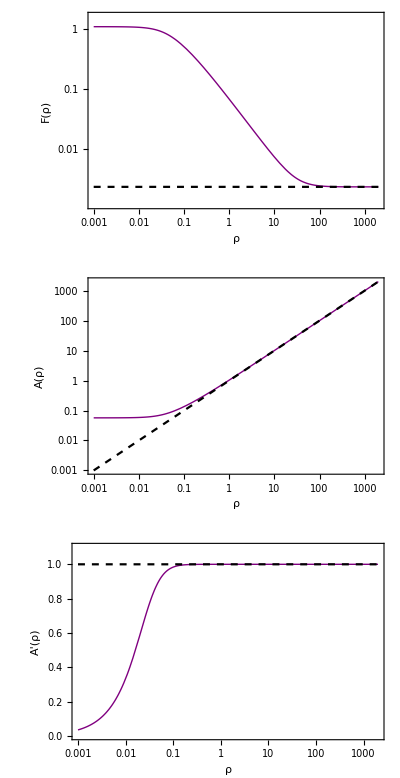

```mathematica
MakePlot[] (* Plot the results *)
```